## Gaussian distribution

Here we produce mean and variance of a Gaussian distribution

```mathematica
g[x_,x0_,σ_]:=Exp[-(x-x0)^2/(2σ^2)]
```

### Normalization

Normalizing the distribution

```mathematica
a=1/Integrate[g[x,x0,σ],{x,-∞,∞},Assumptions->{σ>0}](*Normalization coeficient*)
gauss2[x_,x0_,σ_]=a*g[x,x0,σ]
(*gauss[x_,x0_,σ_]=a*Exp[-(x-x0)^2/(2σ^2)]*)
Print[" Test normalization = ",Integrate[gauss2[x,x0,σ],{x,-∞,∞},Assumptions->{σ>0}]]
```

1/(√(2 π) σ)

(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)

Test normalization = 1

### Mean

```mathematica
mean=Integrate[x*gauss[x,x0,σ],{x,-∞,∞},Assumptions->{σ>0}]
```

x0

### Variance

```mathematica
variance=Integrate[(x-mean)^2*gauss[x,x0,σ],{x,-∞,∞},Assumptions->{σ>0}]
```

σ^2

### Plotting

```mathematica
Manipulate[Plot[gauss[x,a,2],{x,-10,10},PlotStyle->{Thick,Red},Filling->Bottom],{a,-2,2}]
```

```mathematica
Manipulate[Plot[gauss[x,0,a],{x,-10,10},PlotStyle->{Thick,Red},Filling->Bottom,PlotRange->All],{a,0.3,5}]
```

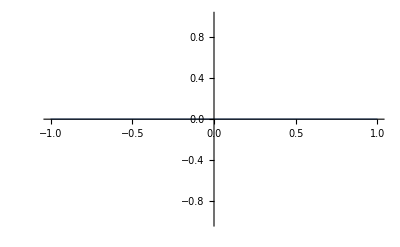

```mathematica
Plot[DiracDelta[x],{x,-1,1},PlotRange->All,PlotStyle->Thick]
```